# ENTROPY CALCULATIONS

## Basics

The first line makes mathematica arrays look like matrices at the outputs. 

The rest is a function that traces out a subsystem of quDits from a N-quDit system. dTraceSystem has 3 arguments, the density matrix ρ, the list of qudits to trace out, 
 e.g. {2, 3} and the dimension d of the qudits. This code was taken from the Wolfram Library Archive and it is called “Partial Trace of a MultiquDit System” by Mark Tame.
(https://library.wolfram.com/infocenter/MathSource/8763/)

```mathematica
ClearAll["Global`*"]
$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
dTraceSystem[D_, s_, dimen_]:= (

Qudits=Reverse[Sort[s]];
TrkM=D;
dim=dimen;

z=(Dimensions[Qudits][[1]]+1);

For[q=1,q<z,q++,
n=Log[dim,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qudits[[q]];
If[k==n,
TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
 ],

For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<dim^n+1,i++,
If[IntegerDigits[i-1,dim,n][[n]]≠IntegerDigits[i-1,dim,n][[n-j-1]] && Count[b, i]  ==0, 
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)];
c=Range[dim^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)}];
M=M[[perm,perm]];
 ]    
];
   ];

TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
]
]
]

;Return[TrkM])
```

## Functions for Entropies

```mathematica
vonNeummanbeta[rho_]:=(
{valsss,vecsss}=Refine[Eigensystem[rho]];
Mss=Refine[Transpose[vecsss]];
Inverse[Mss];
DG=Refine[DiagonalMatrix[vals]];
F[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FD=Refine[MatrixFunction[F,DG]];
Return[ Simplify[-Tr[M.FD.Inverse[M]]]];
)
vonNeumann[densmatr_]:=(
Fv2s[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
Return[Simplify[-Tr[MatrixFunction[Fv2s,densmatr]]]])

ConditionalS[densmatr_,sublist_]:=Simplify[vonNeumann[densmatr]-vonNeumann[dTraceSystem[densmatr,sublist,2]]];
Renyi[denmatr_,a_]:=(
Functionaling[x_]:=x^a ;
matrixtrans=Refine[MatrixFunction[Functionaling,denmatr]];
Return[Simplify[(1/(1-a))Log[Tr[matrixtrans]]]];
)

Unified[densmatr_,r_,s_]:= (Tr[densmatr^r]^s-1)/(s-r*s);

Tsalis[densmatr_,r_]:=(
{valsT,vecsT}=Refine[Eigensystem[densmatr]];
MT=Refine[Transpose[vecsT]];
Inverse[MT];
DGT=Refine[DiagonalMatrix[valsT]];
FT[x_]:=Piecewise[{{x^r,x≥0}},null];
FDT=Refine[MatrixFunction[FT,DGT]];
Return[ Simplify[(Tr[MT.FDT.Inverse[MT]]-1)/(1-r)]];
);
QuadraticEntropy[densmatr_]:=(
{valsQ,vecsQ}=Refine[Eigensystem[densmatr]];
M=Refine[Transpose[vecsQ]];
Inverse[M];
DGQ=Refine[DiagonalMatrix[valsQ]];
FQ[x_]:=Piecewise[{{x^2,x≥0}},null];
FDQ=Refine[MatrixFunction[FQ,DGQ]];
Return[ Simplify[1-Tr[M.FDQ.Inverse[M]]]];
);
ConditionalQ[densmatr_,sublist_]:=Simplify[QuadraticEntropy[densmatr]-QuadraticEntropy[dTraceSystem[densmatr,sublist,2]]];

RelativeEntropy[dm1_,dm2_]:=(
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];
matr=dm1.MatrixFunction[K,dm2];
termo=-Tr[matr]-vonNeumann[dm1];
Return[Simplify[Limit[termo,ε-> -Infinity]]]
)
```

## Calculation Details

### vonNeumman1

```mathematica
psi=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}}
rho=KroneckerProduct[psi1,ConjugateTranspose[psi1]]
{vals,vecs}=Eigensystem[rho1]
M=Transpose[vecs1]
Det[M1]
Inverse[M]
DG=DiagonalMatrix[vals]
M.DG.Inverse[M]==rho;
F[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FD=MatrixFunction[F,DG]
-Tr[M.FD.Inverse[M]]
```

(0
1/(√2)
-ⅈ/(√2)
0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

{{1,0,0,0},{{0,ⅈ,1,0},{0,0,0,1},{0,-ⅈ,1,0},{1,0,0,0}}}

(0 | 0 | 0 | 1
ⅈ | 0 | -ⅈ | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 0)

2 ⅈ

(0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 1
0 | ⅈ/2 | 1/2 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

### vonNeumann2

(s | 0
0 | 1-s)

{{1-s,s},{{0,1},{1,0}}}

(s Log[s] | 0
0 | (1-s) Log[1-s])

-(1-s) Log[1-s]-s Log[s]

True

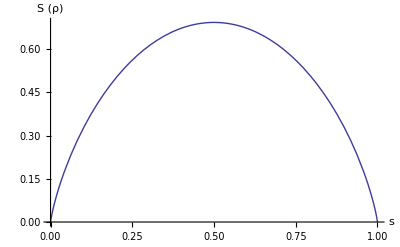

```mathematica
$Assumptions = s∈ Reals && 0<s<1;
rho=Refine[{{s,0},{0,1-s}}]
{vals,vecs}=Refine[Eigensystem[rho]]
F[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FD=Refine[MatrixFunction[F,rho]]
L=-Tr[FD]
Plot[L,{s,0,1},AxesLabel->{"s", "S (ρ)" }]
```

### ConditionalEntropy3

(Cos[θ]
0
0
Sin[θ])

(Cos[θ]^2 | 0 | 0 | Cos[θ] Sin[θ]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2)

{{1,0,0,0},{{(-1+Csc[θ]^2) Tan[θ],0,0,1},{-Tan[θ],0,0,1},{0,0,1,0},{0,1,0,0}}}

(Cot[θ] | -Tan[θ] | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 1 | 0 | 0)

-Csc[θ] Sec[θ]

(Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2
-Cos[θ] Sin[θ] | 0 | 0 | Cos[θ]^2
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

(Cos[θ]^2 | 0
0 | Sin[θ]^2)

(Cos[θ]^2 Log[Cos[θ]^2] | 0
0 | Log[Sin[θ]^2] Sin[θ]^2)

2 (Cos[θ]^2 Log[Cos[θ]]+Log[Sin[θ]] Sin[θ]^2)

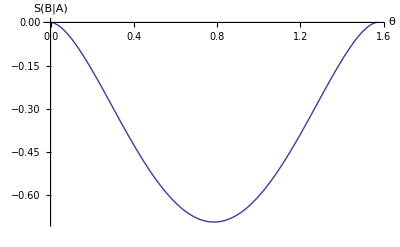

-Log[2]

```mathematica
Clear[θ]
$Assumptions=θ∈Reals && 0<θ<π/2;
chi={{Cos[θ]},{0},{0},{Sin[θ]}}
sigma=Refine[KroneckerProduct[chi,ConjugateTranspose[chi]]]
{values,vecs}=Eigensystem[sigma]
M=Simplify[Transpose[vecs]]
FullSimplify[Det[M]]
Minv=Simplify[Inverse[M]]
diag=DiagonalMatrix[values]
sigma== M.diag.Minv
sigmaA=dTraceSystem[sigma,{2},2]
F[x_]:=x*Log[x];
L=MatrixFunction[F,sigmaA]
FullSimplify[L3=Tr[L]]
Plot[L3,{θ,0,π/2},AxesLabel->{"θ","S(B|A)"}]
Refine[L3,θ== π/4]
```

### Renyi4

```mathematica
$Assumptions = α∈ Reals && α>0 && α≠ 1;
psi=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}}
rho=KroneckerProduct[psi,ConjugateTranspose[psi]]
{vals,vecs}=Eigensystem[rho]
M=Transpose[vecs]
Det[M]
Inverse[M]
DG=DiagonalMatrix[vals]
M.DG.Inverse[M]==rho
F[x_]:=x^α;
matrixtrans=Refine[MatrixFunction[F,DG]]
matrixtransnext=M.matrixtrans.Inverse[M]
L=Tr[matrixtransnext]
Log[L]
```

(0
1/(√2)
-ⅈ/(√2)
0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

{{1,0,0,0},{{0,ⅈ,1,0},{0,0,0,1},{0,-ⅈ,1,0},{1,0,0,0}}}

(0 | 0 | 0 | 1
ⅈ | 0 | -ⅈ | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 0)

2 ⅈ

(0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 1
0 | ⅈ/2 | 1/2 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

1

0

### Renyi5

(s | 0
0 | 1-s)

(s^α | 0
0 | (1-s)^α)

Log[(1-s)^α+s^α]/(1-α)

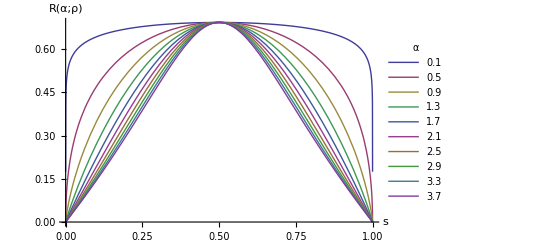

-Graphics3D-

```mathematica
Clear[α,s]
$Assumptions = α∈ Reals && α>0 && α≠ 1;
$Assumptions = s∈ Reals && 0<s<1;
rho= {{s,0},{0,1-s}}
function[x_]:=x^α
finalmatrix=MatrixFunction[function,rho]
L=Log[Tr[finalmatrix]]/(1-α)
Plot[Evaluate@Table[L,{α,0.1,4,0.4}],{s,0,1},PlotLegends->LineLegend[Table[α,{α,0.1,4,0.4}],LegendLabel->α],AxesLabel->{"s","R(α;ρ)"}]
Plot3D[L,{s,0,1},{α,0,15},AxesLabel->{"s","α","R"}]
```

### Tsallis7

```mathematica
Clear[q];
$Assumptions = q∈ Reals && q>0 && q≠ 1;
psi=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}};
rho=KroneckerProduct[psi,ConjugateTranspose[psi]];
{vals,vecs}=Eigensystem[rho]
M=Transpose[vecs]
Det[M]
Inverse[M]
DG=DiagonalMatrix[vals]
M.DG.Inverse[M]==rho
t[x_]:=x^q;
FD=Simplify[MatrixFunction[t,DG]]
trace=Tr[M.FD.Inverse[M]]
(trace-1)/(1-q)
```

{{1,0,0,0},{{0,ⅈ,1,0},{0,0,0,1},{0,-ⅈ,1,0},{1,0,0,0}}}

(0 | 0 | 0 | 1
ⅈ | 0 | -ⅈ | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 0)

2 ⅈ

(0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 1
0 | ⅈ/2 | 1/2 | 0
1 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

True

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

1

0

### Tsallis8

(s | 0
0 | 1-s)

(s^q | 0
0 | (1-s)^q)

(-1+(1-s)^q+s^q)/(1-q)

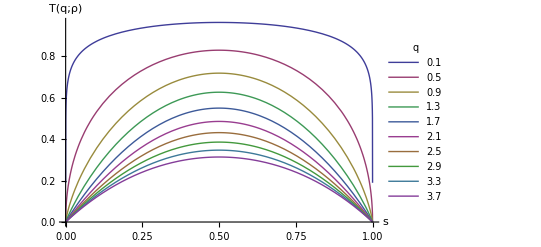

-Graphics3D-

```mathematica
Clear[q,s]
$Assumptions = q∈ Reals && q>0 && q≠ 1;
$Assumptions = s∈ Reals && 0<s<1;
rho= {{s,0},{0,1-s}}
function[x_]:=x^q
matr=MatrixFunction[function,rho]
L=((Tr[matr])-1)/(1-q)
Plot[Evaluate@Table[L,{q,0.1,4,0.4}],{s,0,1},PlotLegends->LineLegend[Table[q,{q,0.1,4,0.4}],LegendLabel->q],AxesLabel->{"s","T(q;ρ)"}]
Plot3D[L8,{s,0,1},{q,0,15},AxesLabel->{"s","q","T"}]
```

### WernerStateConditional

-Log[2]+3/4 (-1+s) Log[(1-s)/4]-1/4 (1+3 s) Log[1/4 (1+3 s)]

0.747614

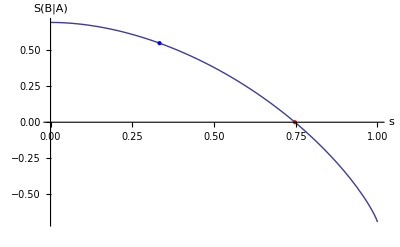

```mathematica
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
{Wvals,Wvecs}=Eigensystem[WernerState];
Mw=Refine[Transpose[Wvecs]];
Det[Mw];
Inverse[Mw];
DGw=Refine[DiagonalMatrix[Wvals]];
WernerState==Simplify[Mw.DG.Inverse[Mw]];
Fw[x_]:=Piecewise[{{x*Log[x],x>0},{0,x==0}},null];
FDw=Refine[MatrixFunction[Fw,DGw]];

Simplify[-Tr[Mw.FDw.Inverse[Mw]]]==Simplify[vonNeumann[WernerState]];
Simplify[vonNeumann[WernerState]];
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];
CSofWerner=vonNeumann[WernerState]-vonNeumann[WernerStateA]
Entanglementsvalue=N[Refine[CSofWerner,s==1/3]];
N[Refine[vonNeumann[WernerStateA],s==1/3]];
zerocondwerner=s/.FindRoot[CSofWerner,{s,0.7}]

plot1=Plot[CSofWerner,{s,0,1},AxesLabel->{"s","S(B|A)"},GridLines->{{{1/3,Dashed}},{{Entanglementsvalue,Dashed}}},Epilog->{{Blue,PointSize@Large,Point[{1/3,Entanglementsvalue}]},{Red,PointSize@Large,Point[{zerocondwerner,0}]}}]
```

### WernerStateConditionalTsallis

(2^(-1-x) (2^(1+x)-3 (1-s)^x-(1+3 s)^x))/(-1+x)

-Graphics3D-

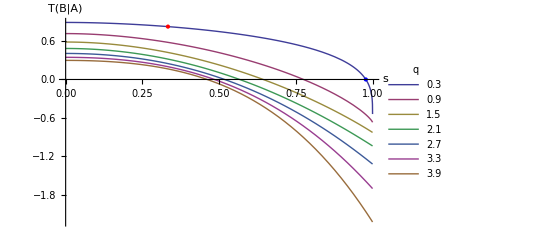

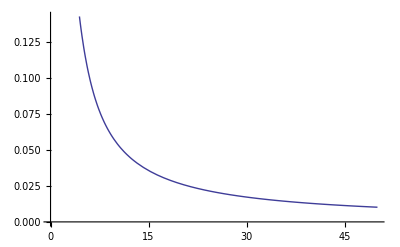

```mathematica
Clear[s,x,q];
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];

{valsT,vecsT}=Refine[Eigensystem[WernerState]];
MT=Refine[Transpose[vecsT]];
Inverse[MT];
DGT=Refine[DiagonalMatrix[valsT]];
FT[y_]:=Piecewise[{{y^x,y≥0}},null];
FDT=Refine[MatrixFunction[FT,DGT]];
MT.FDT.Inverse[MT];

Firstterm=(Tr[MT.FDT.Inverse[MT]]-1)/(1-x);

FDT2=Refine[MatrixFunction[FT,WernerStateA]];
Secondterm=(Tr[FDT2]-1)/(1-x);
ResultingT=Simplify[(Firstterm-Secondterm)/(1+(1-x)*Secondterm)]
Plot3D[ResultingT,{x,0,3},{s,0,1}]

examplidionT1=Refine[ResultingT,x==0.3];
root1=s/.FindRoot[examplidionT1,{s,0.9}];
examplidionT2=Refine[ResultingT,x==0.9];
root2=s/.FindRoot[examplidionT2,{s,0.9}];
examplidionT3=Refine[ResultingT,x==1.5];
root3=s/.FindRoot[examplidionT3,{s,0.9}];
examplidionT4=Refine[ResultingT,x==2.1];
root4=s/.FindRoot[examplidionT4,{s,0.9}];
examplidionT5=Refine[ResultingT,x==2.7];
root5=s/.FindRoot[examplidionT5,{s,0.9}];
examplidionT6=Refine[ResultingT,x==3.3];
root6=s/.FindRoot[examplidionT6,{s,0.9}];
examplidionT7=Refine[ResultingT,x==3.9];
root7=s/.FindRoot[examplidionT7,{s,0.9}];

Root1=examplidionT1/.s->1/3;
Root2=examplidionT2/.s->1/3;
Root3=examplidionT3/.s->1/3;
Root4=examplidionT4/.s->1/3;
Root5=examplidionT5/.s->1/3;
Root6=examplidionT6/.s->1/3;
Root7=examplidionT7/.s->1/3;
Clear[q]
Plot[Evaluate@Table[ResultingT,{x,0.3,4,0.6}],{s,0,1},PlotLegends->LineLegend[Table[x,{x,0.3,4,0.6}],LegendLabel->q],AxesLabel->{"s","T(B|A)"},GridLines->{{{1/3,Dashed}},{{Root1,Dashed}}},Epilog->{{Red,PointSize[Large],Point[{1/3,Root1}]},{Blue,PointSize[Large],Point[{root1,0}]}}]
EntanglementLimitValueT=Refine[ResultingT,s==1/3];
Plot[EntanglementLimitValueT,{x,0,50}]
```

### WernerStateConditionalRenyi

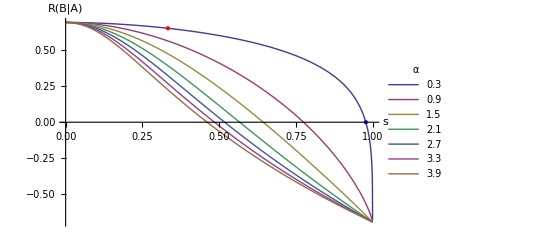

(Log[2^(1-α)]-Log[4^-α (2^α+2^α 3^(1-α))])/(-1+α)

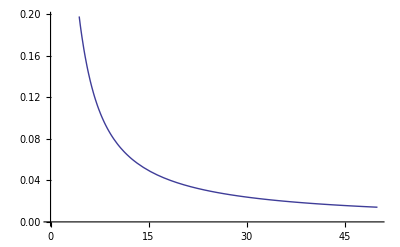

-Graphics3D-

```mathematica
Clear[α,s]
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
WernerStateA= Simplify[dTraceSystem[WernerState,{2},2]];
CRofWerner=FullSimplify[Renyi[WernerState,α]-Renyi[WernerStateA,α]];
Clear[α]
{valsR,vecsR}=Refine[Eigensystem[WernerState]];
MR=Refine[Transpose[vecsR]];
Inverse[MR];
DGR=Refine[DiagonalMatrix[valsR]];
FR[y_]:=Piecewise[{{y^α,y≥0}},null];
FDR=Refine[MatrixFunction[FR,DGR]];
FDR;
FtermR=Simplify[Log[Tr[MR.FDR.Inverse[MR]]]/(1-α)];
FDR=Refine[MatrixFunction[FR,WernerStateA]];
FDR;
StermR=Simplify[Log[Tr[FDR]]/(1-α)];
ttt=Simplify[FtermR-StermR];

examplidionR1=Refine[CRofWerner,α==0.3];
Rroot1=s/.FindRoot[examplidionR1,{s,0.9}];
Root1=examplidionR1/.s->1/3;

Plot[Evaluate@Table[ttt,{α,0.3,4,0.6}],{s,0,1},PlotLegends->LineLegend[Table[α,{α,0.3,4,0.6}],LegendLabel->α],AxesLabel->{"s","R(B|A)"},GridLines->{{{1/3,Dashed}},{{Root1,Dashed}}},Epilog->{{Red,PointSize[Large],Point[{1/3,Root1}]},{Blue,PointSize[Large],Point[{Rroot1,0}]}}]


examplidionS=Refine[CRofWerner,α==0.3];
s/.FindRoot[examplidionS,{s,0.9}];

EntanglementLimitValue=Refine[CRofWerner,s==1/3]
Plot[EntanglementLimitValue,{α,0,50}]
Plot3D[ttt,{α,0,3},{s,0,1}]
```

### Relative entropy6

```mathematica
psi6=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}}
rho6=KroneckerProduct[psi6,ConjugateTranspose[psi6]]
sigma6= {{1/2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1/2}}
Eigensystem[sigma6]
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];
matr6g=MatrixFunction[K,sigma6]
matrix6=rho6.matr6g
L9=-Limit[Tr[matrix6],ε-> -Infinity]
L9== RelativeEntropy[rho6,sigma6]
RelativeEntropy[sigma6,rho6]
```

(0
1/(√2)
-ⅈ/(√2)
0)

(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

(1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/2)

{{1/2,1/2,0,0},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}

(-Log[2] | 0 | 0 | 0
0 | ε | 0 | 0
0 | 0 | ε | 0
0 | 0 | 0 | -Log[2])

(0 | 0 | 0 | 0
0 | ε/2 | (ⅈ ε)/2 | 0
0 | -(ⅈ ε)/2 | ε/2 | 0
0 | 0 | 0 | 0)

∞

True

∞

### Relative(Pure-Pure)

```mathematica
Clear[t,u,psi,rho]
$Assumptions=t∈Reals && 0<t<π/2;
$Assumptions=u∈Reals && 0<u<π/2;
psit={{Cos[t]},{0},{0},{Sin[t]}};
rhot=Refine[KroneckerProduct[psit,ConjugateTranspose[psit]],t∈Reals ]
psi={{Cos[u]},{0},{0},{Sin[u]}};
rho=Refine[KroneckerProduct[psi,ConjugateTranspose[psi]]]
Kappa[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];

{valst,vecst}=FullSimplify[Refine[Eigensystem[rhot]]]
Mt=FullSimplify[Refine[Transpose[vecst]]]
DGt=Refine[DiagonalMatrix[valst]]
InveMt=FullSimplify[Inverse[Mt]]

Mt.MatrixFunction[Kappa,DGt].InveMt
FullSimplify[Tr[rho.Simplify[MatrixFunction[Kappa,rhot]]]]

Mt.MatrixFunction[Kappa,DGt].InveMt/.t-> u
FullSimplify[Tr[rho.Simplify[MatrixFunction[Kappa,rhot]]]]
```

(Cos[t]^2 | 0 | 0 | Cos[t] Sin[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
Cos[t] Sin[t] | 0 | 0 | Sin[t]^2)

(Cos[u]^2 | 0 | 0 | Cos[u] Sin[u]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
Cos[u] Sin[u] | 0 | 0 | Sin[u]^2)

{{1,0,0,0},{{Cot[t],0,0,1},{-Tan[t],0,0,1},{0,0,1,0},{0,1,0,0}}}

(Cot[t] | -Tan[t] | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
1 | 1 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(Cos[t] Sin[t] | 0 | 0 | Sin[t]^2
-Cos[t] Sin[t] | 0 | 0 | Cos[t]^2
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

(ε Sin[t]^2 | 0 | 0 | -ε Cos[t] Sin[t]
0 | ε | 0 | 0
0 | 0 | ε | 0
-ε Cos[t] Sin[t] | 0 | 0 | ε Cos[t]^2)

ε Sin[t-u]^2

(ε Sin[u]^2 | 0 | 0 | -ε Cos[u] Sin[u]
0 | ε | 0 | 0
0 | 0 | ε | 0
-ε Cos[u] Sin[u] | 0 | 0 | ε Cos[u]^2)

ε Sin[t-u]^2

RelativeEntropy[{{Cos[u]^2,0,0,Cos[u] Sin[u]},{0,0,0,0},{0,0,0,0},{Cos[u] Sin[u],0,0,Sin[u]^2}},{{Cos[t]^2,0,0,Cos[t] Sin[t]},{0,0,0,0},{0,0,0,0},{Cos[t] Sin[t],0,0,Sin[t]^2}}]

### Relative(Werner from Maximally Mixed)(Mixed-Mixed)

(0 | 0 | 1 | 0
0 | -ⅈ | 0 | ⅈ
0 | 1 | 0 | 1
1 | 0 | 0 | 0)

(0 | 0 | 0 | 1
0 | ⅈ/2 | 1/2 | 0
1 | 0 | 0 | 0
0 | -ⅈ/2 | 1/2 | 0)

((1-s)/4 | 0 | 0 | 0
0 | (1-s)/4 | 0 | 0
0 | 0 | (1-s)/4 | 0
0 | 0 | 0 | 1/4 (1+3 s))

True

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4)

1/4 (-3 (-1+s) Log[1-s]+(1+3 s) Log[1+3 s])

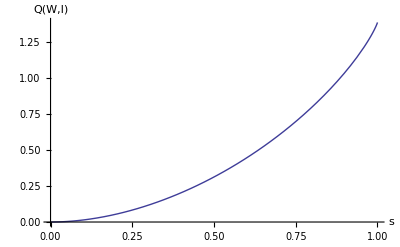

1/4 (-3 Log[1-s]-Log[1+3 s])

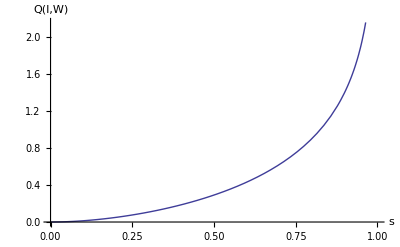

```mathematica
$Assumptions=s∈Reals && 0<s<1;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};
psi1=(1/Sqrt[2])*{{0},{1},{-ⅈ},{0}};
rho1=KroneckerProduct[psi1,ConjugateTranspose[psi1]];
WernerState2=Simplify[(1-s)*IdentityMatrix[4]/4+s*rho1];
{Wvals,Wvecs}=Eigensystem[WernerState2];
Mw=Refine[Transpose[Wvecs]]
Inverse[Mw]
DGw=Refine[DiagonalMatrix[Wvals]]
WernerState2==Simplify[Mw.DGw.Inverse[Mw]]

MaximallyMixed=IdentityMatrix[4]/4
testcase1=RelativeEntropy[WernerState2,MaximallyMixed]
Plot[testcase1,{s,0,1},AxesLabel->{"s","Q(W,I)"}]
testcase2=RelativeEntropy[MaximallyMixed,WernerState2]
Plot[testcase2,{s,0,1},AxesLabel->{"s","Q(I,W)"}]
```

### Relative(Pure-Mixed)(Werner-Entangled State)II

1/2 (Log[16/(1+2 s-3 s^2)]+Log[(1-s)/(1+3 s)] Sin[2 θ])

∞

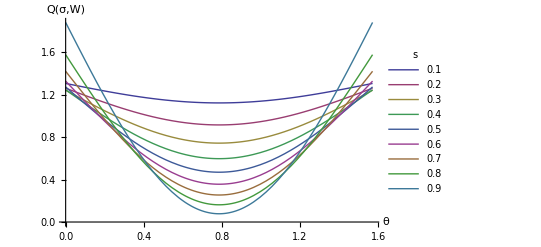

-Graphics3D-

```mathematica
Clear[s,θ,chi,sigma,WernerState,WernerState2,chi3,sigma3,WernerState2]
$Assumptions=s∈Reals && 0<s<1 && θ∈Reals && 0<θ<π/2;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};

chi={{Cos[θ]},{0},{0},{Sin[θ]}};
sigma=Refine[KroneckerProduct[chi,ConjugateTranspose[chi]]];

case=RelativeEntropy[sigma,WernerState]
RelativeEntropy[WernerState,sigma]
Plot[Evaluate@Table[case,{s,0.1,0.9,0.1}],{θ,0,π/2},PlotLegends->LineLegend[Table[s,{s,0.1,0.9,0.1}],LegendLabel->s],AxesLabel->{"θ","Q(σ,W)"},GridLines->{{{π/4,Dashed}},None}]
Plot3D[case,{s,0,1},{θ,0,π/2}]
```

## Others

### Quadratic Conditional

(-1+Cos[θ]^4+Sin[θ]^4)

-Graphics-

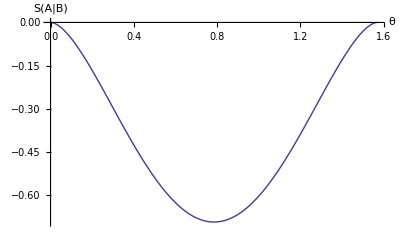

-Graphics-

```mathematica
Clear[θ,L3,L4,t]
$Assumptions=θ∈Reals && 0<θ<π/2;
chi3={{Cos[θ]},{0},{0},{Sin[θ]}};
sigma3=Refine[KroneckerProduct[chi3,ConjugateTranspose[chi3]]];
{values3,vecs3}=Simplify[Eigensystem[sigma3]];
M3=Simplify[Transpose[vecs3]];
FullSimplify[Det[M3]];
M3inv=Simplify[Inverse[M3]];
diag3=DiagonalMatrix[values3];
sigma3== M3.diag3.M3inv;
vonNeumann[sigma3];
sigma3A=dTraceSystem[sigma3,{2},2];
L3=ConditionalS[sigma3,{2}];
L4 =Refine[Tsalis[sigma3,t]-Tsalis[sigma3A,t],t==2]
p4=Plot[L4,{θ,0,π/2},AxesLabel->{"θ","QS(A|B)"}]
p3=Plot[L3,{θ,0,π/2},AxesLabel->{"θ","S(A|B)"}]
Refine[L3,θ== π/4];
Show[p3,p4]
```

### Relative Entropy Example(Mixed-Mixed)

```mathematica
Clear[s1,s2,t,rho2,L,sigma2]
$Assumptions = s1∈ Reals && 0<s1<1;
$Assumptions = s2∈ Reals && 0<s2<1;
ket0={{1},{0}};
bra0=ConjugateTranspose[ket0];
ket1={{0},{1}};
bra1=ConjugateTranspose[ket1];
ket00=KroneckerProduct[ket0,ket0];
bra00=ConjugateTranspose[ket00];
ket01=KroneckerProduct[ket0,ket1];
bra01=ConjugateTranspose[ket01];
ket10=KroneckerProduct[ket1,ket0];
bra10=ConjugateTranspose[ket01];
ket11=KroneckerProduct[ket1,ket1];
bra11=ConjugateTranspose[ket11];
rho2=s1*(ket0.bra0)+(1-s1)*(ket1.bra1)
sigma2=s2*(ket0.bra0)+(1-s2)*(ket1.bra1)
K[x_]:=Piecewise[{{Log[x],x>0},{ε,x==0}},null];

secondmatrix=Simplify[MatrixFunction[K,sigma2]]
secondterm = Tr[rho2.secondmatrix]
firstterm = Refine[vonNeumann[rho2],0<s1<1]
L8=firstterm-secondterm
Plot3D[L8,{s1,0,1},{s2,0,1}]

secondmatrix2=Refine[MatrixFunction[K,rho2],0<s1<1]
secondterm2= Tr[sigma2.secondmatrix]
firstterm2 = Refine[vonNeumann[sigma2],0<s2<1]
L82=firstterm2-secondterm2

Refine[RelativeEntropy[rho2,sigma2]]
```

(s1 | 0
0 | 1-s1)

(s2 | 0
0 | 1-s2)

(Log[s2] | 0
0 | Log[1-s2])

(1-s1) Log[1-s2]+s1 Log[s2]

(-1+s1) Log[1-s1]-s1 Log[s1]

(-1+s1) Log[1-s1]-s1 Log[s1]-(1-s1) Log[1-s2]-s1 Log[s2]

-Graphics3D-

(Log[s1] | 0
0 | Log[1-s1])

(1-s2) Log[1-s2]+s2 Log[s2]

(-1+s2) Log[1-s2]-s2 Log[s2]

-(1-s2) Log[1-s2]+(-1+s2) Log[1-s2]-2 s2 Log[s2]

### RelativeEntropy example (Pure - Pure)

```mathematica
ket0={{1},{0}};
bra0=ConjugateTranspose[ket0];
ket1={{0},{1}};
bra1=ConjugateTranspose[ket1];
ket00=KroneckerProduct[ket0,ket0];
bra00=ConjugateTranspose[ket00];
ket01=KroneckerProduct[ket0,ket1];
bra01=ConjugateTranspose[ket01];
ket10=KroneckerProduct[ket1,ket0];
bra10=ConjugateTranspose[ket01];
ket11=KroneckerProduct[ket1,ket1];
bra11=ConjugateTranspose[ket11];
```

```mathematica
Clear[s,θ,chi,sigma,WernerState,WernerState2,chi3,sigma3,WernerState2]
$Assumptions=s∈Reals && 0<s<1 && θ∈Reals && 0<θ<π/2;
WernerState={{(1+s)/4,0,0,s/2},{0,((1-s)/4),0,0},{0,0,(1-s)/4,0},{s/2,0,0,(1+s)/4}};

chi={{Cos[θ]},{0},{0},{Sin[θ]}};
sigma=Refine[KroneckerProduct[chi,ConjugateTranspose[chi]]]

case=RelativeEntropy[sigma,WernerState]

Plot[Evaluate@Table[case,{s,0.1,0.9,0.1}],{θ,0,π/2},PlotLegends->LineLegend[Table[s,{s,0.1,0.9,0.1}],LegendLabel->s],AxesLabel->{"θ","Q(σ,W)"},GridLines->{{{π/4,Dashed}},None}]
```